```mathematica
transformation = LinearFractionalTransform[{{a,b,c},{e,f,g},{h,i,j}}]
PNEW = {(a x + b y + c)/(h x + i y + j),(e x + f y + g)/(h x + i y + j)}
```

TransformationFunction[(a | b | c
e | f | g
h | i | j)]

{(c+a x+b y)/(j+h x+i y),(g+e x+f y)/(j+h x+i y)}

{{1,1},{1,2},{2,1},{2,2}}

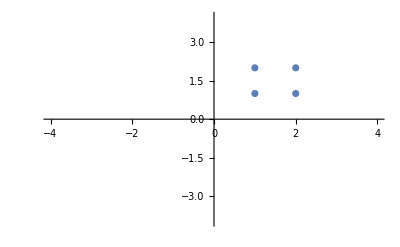

```mathematica
Shape ={{1,1},{1,2},{2,1},{2,2}}
ListPlot[Shape, PlotRange->{{-4,4},{-4,4}}]
```

```mathematica
Newshape = transformation[Shape]
```

{{(a+b+c)/(h+i+j),(e+f+g)/(h+i+j)},{(a+2 b+c)/(h+2 i+j),(e+2 f+g)/(h+2 i+j)},{(2 a+b+c)/(2 h+i+j),(2 e+f+g)/(2 h+i+j)},{(2 a+2 b+c)/(2 h+2 i+j),(2 e+2 f+g)/(2 h+2 i+j)}}

```mathematica
ClearAll[outCircle,inCircle]
Needs["ComputationalGeometry`"];
outCircle[Polygon[a_]]:=outCircle[Flatten[a,Depth[a]-3]];
outCircle[points_List]:=outCircle[points]=Module[{calcDisk,moveToFront,circleThrough3Points},circleThrough3Points[{p1_,p2_,p3_}]:=Module[{ax,ay,bx,by,cx,cy,a,b,c,d,e,f,g,centerx,centery,r},{ax,ay}=p1;
{bx,by}=p2;
{cx,cy}=p3;
a=bx-ax;
b=by-ay;
c=cx-ax;
d=cy-ay;
e=a (ax+bx)+b (ay+by);
f=c (ax+cx)+d (ay+cy);
g=2 (a (cy-by)-b (cx-bx));
If[g==0,False,{centerx=(d e-b f)/g,centery=(a f-c e)/g,r=Sqrt[(ax-centerx)^2+(ay-centery)^2]}];
{{centerx,centery},r}];
calcDisk[{}]:={0,0};
calcDisk[{{x_,y_}}]:={0,0};
calcDisk[{{x_,y_},{x2_,y2_}}]:={Mean[{{x,y},{x2,y2}}],Norm[{x,y}-{x2,y2}]/2};
calcDisk[{{x_,y_},{x2_,y2_},{x3_,y3_}}]:=circleThrough3Points[{{x,y},{x2,y2},{x3,y3}}];
moveToFront[pts_,b_]:=Module[{copy=pts,c,rs},{c,rs}=calcDisk[b];
If[Length@b≠3,Do[If[Norm[copy[[n]]-c]>rs,{c,rs}=moveToFront[copy[[;;n-1]],Union[b,copy[[{n}]]]];
copy=Prepend[Delete[copy,n],copy[[n]]]],{n,Length@pts}]];
{c,rs}];
moveToFront[points,{}]];
```

```mathematica
outCircle[Shape]
inCircle[Shape]
lower = -5
upper = 5
Manipulate[{ListPlot[Newshape/.{a->p,b->q,c->r,e->t,f->u,g->v,h->w,i->z, j -> o},PlotRange->{{-10,10},{-10,10}}],Last[inCircle[Newshape/.{a->p,b->q,c->r,e->t,f->u,g->v,h->w,i->z, j -> o}]]/Last[outCircle[Newshape/.{a->p,b->q,c->r,e->t,f->u,g->v,h->w,i->z, j -> o}]]},{{p,1},lower,5}, {{q,0},lower,5}, {{r,0},-5,5},{{t,0},-5,5}, {{u,1},-5,5}, {{v,0},-5,5}, {{w,0},-5,5}, {{z,0},-5,5}, {{o,1},-5,5}]
```

{{3/2,3/2},1/(√2)}

{{1.79289,1.5},0.207107}

-5

5

{{3/2,3/2},1/(√2)}

{Last[{}],Min[√2 Abs[-2+Last[{}]],√2 Abs[-1+Last[{}]],√(Abs[-2+Last[{}]]^2+Abs[-1+Last[{}]]^2)]}

-5

5

```mathematica
Simplify[{{x1,x2}}.{{2,1},{1,1}}.{y1,y2}]
```

{x2 (y1+y2)+x1 (2 y1+y2)}

```mathematica
MatrixForm[{{x1},{x2}}]
```

(x1
x2)